## Perturbation Theory Kinetic Energy

### Overview

#### Sample Case

In our perturbation theory Hamiltonian we have lots of terms that look like

p_i k_ij p_j

where k_ij is some G matrix element.

We then have matrix elements that end up looking like:

n p_i k_ij p_j m =k_ij n p_i p_j m

where n and m are just products of harmonic oscillator eigenstates in all of our coordinates of interest.

Clearly, many of these terms will be zero and having an efficient strategy for building these matrices will allow us to more cleanly and quickly obtain our perturbation theory energies and wavefunctions

#### Raising and Lowering form of p

Since we have harmonic oscillators, we can just write this in terms of raising and lowering operators. Recalling that:

a = √(mω/(2ℏ))(x + i/mω p)
a^† = √(mω/(2ℏ))(x - i/mω p)

we have

2 √(mω/(2ℏ))i/mω p=a-a^†

and so

p=1/2 mω/i √((2ℏ)/mω)(a-a^†)
=i √(mωℏ/2)(a^†-a)

p=i √(mωℏ/2)(a^†-a)
x=√(mω/(2ℏ))(a^†+a)

So in total we have:

p_i p_j = (i √((m_i ω_i ℏ)/2)((a^†)_i-a_i))(i √((m_i ω_i ℏ)/2)((a^†)_j-a_j))
=-√((m_i ω_i ℏ)/2)√((m_j ω_j ℏ)/2)((a^†)_i-a_i)((a^†)_j-a_j)
=-√((m_i ω_i ℏ)/2)√((m_j ω_j ℏ)/2)((a^†)_i(a^†)_j-a_i(a^†)_j-(a^†)_i a_j+a_i a_j)

#### Notation

To simplify the writing of these promoted terms and to cut down on the number of little bits to track, we’ll write the raising and lowering coefficients in the same form as the operators. That is we’ll write:

(a^†)_i n=(c^†)_n n+1
a_i n=c_n n-1

### Expressions

#### General Expansion

In the most general case (ignoring the leading constant), we have

n p_i p_j m=-n(a^†)_i(a^†)_j-a_i(a^†)_j-(a^†)_i a_j+a_i a_j m
=-(n(a^†)_i(a^†)_j m - n a_i(a^†)_j m-n(a^†)_i a_j m+n a_i a_j m)

To make this a bit simpler to work with, we’ll consider some simpler cases first

#### 1D Case

If we are in 1D, we only have one basis function and this is pretty simple. We don’t actually have an i or j in our system, so we end up with:

nppm=-(n a^†a^†m - na a^†m-n a^†am+naam)
=-((c^†)_m(c^†)_(m+1)δ_(n,m+2) -((c^†)_m c_(m+1)+c_m(c^†)_(m-1))δ_(n,m)+c_m c_(m-1)δ_(n,m-2))

Clearly, then we get a tridiagonal matrix in n and m

#### 2D Case

If we are in 2D, things are somewhat more complicated as now n and m can have different quantum numbers. We’ll consider two cases here:

Case 1: i=j

If i = j, things reduce to pretty much the same as the 1D case, except now we have things like

n p_i p_i m=-(n(a^†)_i(a^†)_i m - n a_i(a^†)_i m-n(a^†)_i a_i m+n a_i a_i m)
=-((c^†)_m_i(c^†)_(m_i+1)δ_(n_i,m_i+2) -((c^†)_m_i c_(m_i+1)+c_m_i(c^†)_(m_i-1))δ_(n_i,m_i)+c_m_i c_(m_i-1)δ_(n_i,m_i-2))

(note that I only write things like δ_(n_i,m_i+2) but to have a non-zero overlap we need ∀k≠i, n_k=m_k)

Case 2: i≠j

If i ≠ j, we now have to deal with the promotion along each different coordinate

n p_i p_j m=-(n(a^†)_i(a^†)_j m - n a_i(a^†)_j m-n(a^†)_i a_j m+n a_i a_j m)
=-(
	(c^†)_m_i(c^†)_m_j δ_(n_i,m_i+1)δ_(n_j,m_j+1) -
	c_m_i(c^†)_m_j δ_(n_i,m_i-1)δ_(n_j,m_j+1)-
	(c^†)_m_i c_m_j δ_(n_i,m_i+1)δ_(n_j,m_j-1) +
	c_m_i c_m_j δ_(n_i,m_i-1)δ_(n_j,m_j-1)
)

Combined

With these two cases we can now consider the two-by-two block matrix representation of this operator. We have

(P_x P_x | P_x P_y
P_y P_x | P_y P_y)=(0 p_x p_x 0 | ⋯ | 0 p_x p_x N
⋮ | ⋱ | ⋮
N p_x p_x 0 | ⋯ | N p_x p_x N | 0 p_x p_y 0 | ⋯ | 0 p_x p_y N
⋮ | ⋱ | ⋮
N p_x p_y 0 | ⋯ | N p_x p_y N
0 p_y p_x 0 | ⋯ | 0 p_y p_x N
⋮ | ⋱ | ⋮
N p_y p_x 0 | ⋯ | N p_y p_x N | 0 p_y p_y 0 | ⋯ | 0 p_y p_y N
⋮ | ⋱ | ⋮
N p_y p_y 0 | ⋯ | N p_y p_y N)

Our usage of 0 and N disguise some of the structure of this, though. In reality, these are shorthands for:

0=0_x, 0_y
N=N_x, N_y

In our construction of this, we’ll choose to order these things by having x vary the fastest and then y, giving us a progression like:

0_x, 0_y, 1_x, 0_y … N_x, 0_y, 0_x, 1_y, 1_x, 1_y …

This matters for how we actually formulate our matrices.

Next we’ll look at the symmetry of this matrix. We have:

n p_y p_x m=n_x, n_y p_y p_x m_x, m_y
=m_x, m_y p_y p_x n_x, n_y
=m p_y p_x n

So clearly it must also be symmetric (or rather it’s Hermitian, but entirely real)

##### Matrix Formulation

Example Term

With these expressions, now we’ll want to think about how they play out as matrices. Case 1 is easier as we only have one index to worry about so we’ll focus on case 2 where we have things like δ_(n_i,m_i+1)δ_(n_j,m_j-1). Looking at the expected structure, letting i be the fastest changing dimension, we identify the only non-zero terms in the matrix (note that if we had reversed the roles of i and j we would have obtained the transpose of this).

((("i")_11
("j")_11) | (("i")_12
("j")_11) | (("i")_13
("j")_11) | (("i")_11
("j")_12) | (("i")_12
("j")_12) | (("i")_13
("j")_12) | (("i")_11
("j")_13) | (("i")_12
("j")_13) | (("i")_13
("j")_13)
(("i")_21
("j")_11) | (("i")_22
("j")_11) | (("i")_23
("j")_11) | (("i")_21
("j")_12) | (("i")_22
("j")_12) | (("i")_23
("j")_12) | (("i")_21
("j")_13) | (("i")_22
("j")_13) | (("i")_23
("j")_13)
(("i")_31
("j")_11) | (("i")_32
("j")_11) | (("i")_33
("j")_11) | (("i")_31
("j")_12) | (("i")_32
("j")_12) | (("i")_33
("j")_12) | (("i")_31
("j")_13) | (("i")_32
("j")_13) | (("i")_33
("j")_13)
(("i")_11
("j")_21) | (("i")_12
("j")_21) | (("i")_13
("j")_21) | (("i")_11
("j")_22) | (("i")_12
("j")_22) | (("i")_13
("j")_22) | (("i")_11
("j")_23) | (("i")_12
("j")_23) | (("i")_13
("j")_23)
(("i")_21
("j")_21) | (("i")_22
("j")_21) | (("i")_23
("j")_21) | (("i")_21
("j")_22) | (("i")_22
("j")_22) | (("i")_23
("j")_22) | (("i")_21
("j")_23) | (("i")_22
("j")_23) | (("i")_23
("j")_23)
(("i")_31
("j")_21) | (("i")_32
("j")_21) | (("i")_33
("j")_21) | (("i")_31
("j")_22) | (("i")_32
("j")_22) | (("i")_33
("j")_22) | (("i")_31
("j")_23) | (("i")_32
("j")_23) | (("i")_33
("j")_23)
(("i")_11
("j")_31) | (("i")_12
("j")_31) | (("i")_13
("j")_31) | (("i")_11
("j")_32) | (("i")_12
("j")_32) | (("i")_13
("j")_32) | (("i")_11
("j")_33) | (("i")_12
("j")_33) | (("i")_13
("j")_33)
(("i")_21
("j")_31) | (("i")_22
("j")_31) | (("i")_23
("j")_31) | (("i")_21
("j")_32) | (("i")_22
("j")_32) | (("i")_23
("j")_32) | (("i")_21
("j")_33) | (("i")_22
("j")_33) | (("i")_23
("j")_33)
(("i")_31
("j")_31) | (("i")_32
("j")_31) | (("i")_33
("j")_31) | (("i")_31
("j")_32) | (("i")_32
("j")_32) | (("i")_33
("j")_32) | (("i")_31
("j")_33) | (("i")_32
("j")_33) | (("i")_33
("j")_33))

We can then see the block structure in this problem and recast it in a sparse version using Kronecker products

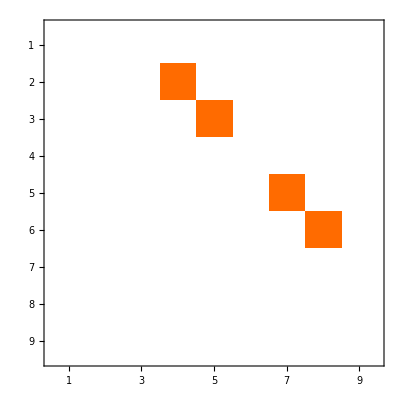

```mathematica
term1= SparseArray[Band[{1, 2}]->1, {3, 3}];
term2=SparseArray[Band[{2, 1}]->1, {3, 3}];
combo=KroneckerProduct[term1, term2];
combo//MatrixPlot
```

This makes it fast to generate big versions of these, too

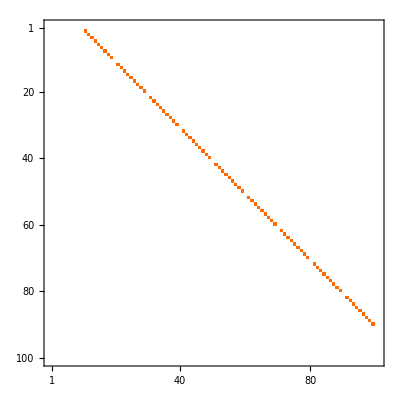

```mathematica
KroneckerProduct[
SparseArray[Band[{1, 2}]->1, {10, 10}], 
SparseArray[Band[{2, 1}]->1, {10, 10}]
]//MatrixPlot
```

This procedure will generalize no matter the number of δ expressions we need to handle.

Full Matrix

We’ll build this entire thing via sparse matrix operations for convenience and speed

```mathematica
c[m_]:=√(m-1);
cP[m_]:=√m;
aMat[n_]:=
SparseArray[
Band[{1,2}]->c[Range[2, n]],
{n, n}
]
aDgMat[n_]:=
SparseArray[
Band[{2,1}]->cP[Range[n-1]],
{n, n}
];
```

```mathematica
(aDgMat[5] - aMat[5])//MatrixForm
```

(0 | -1 | 0 | 0 | 0
1 | 0 | -√2 | 0 | 0
0 | √2 | 0 | -√3 | 0
0 | 0 | √3 | 0 | -2
0 | 0 | 0 | 2 | 0)

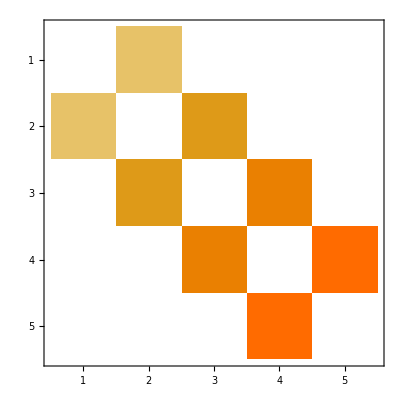

```mathematica
(aMat[5] + aDgMat[5])//MatrixPlot
```

```mathematica
makeMat[coeffs_, dimensions_]:=
ArrayFlatten@
Table[
coeffs[[i]]*coeffs[[j]]*
Fold[
KroneckerProduct,
MapIndexed[
Which[
#2[[1]]==i&&i==j,
MatrixPower[
(aDgMat[#] - aMat[#]),
2
],
#2[[1]]==i||#2[[1]]==j,
aDgMat[#] - aMat[#],
True,
IdentityMatrix[#, SparseArray]
]&,
dimensions(*If[i==j, dimensions, Delete[dimensions, j]]*)
]
],
{i, Range[Length@dimensions]},
{j, Range[Length@dimensions]}
]
```

Here’s an example in 3D with different numbers of basis functions:

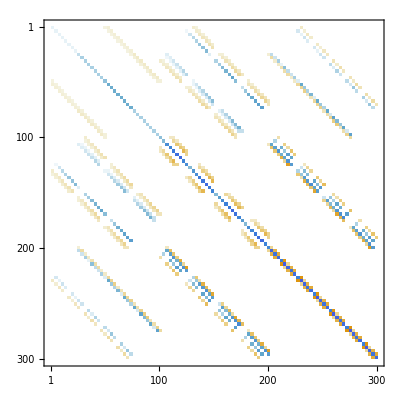

```mathematica
makeMat[{1, 2, 3}, {4, 5, 5}]//MatrixPlot
```

### Full Hamiltonian

Our actual PT Hamiltonian has three bits to it (note that H^(0) is properly 2D but all of the off-diagonal terms are zero)

H^(0) = 1/2∑_i (g_ii p_i p_i+∂^2/(∂Q_i^2)V Q_i Q_i)
H^(1)=1/2∑_(i,j,k) ((∂g_ij)/(∂Q_k)p_i Q_k p_j+1/3∂^3/(∂Q_i∂Q_j∂Q_k)V Q_i Q_j Q_k)
H^(2)=1/4∑_(i,j,kl) ((∂^2 g_ij)/(∂Q_k∂Q_j)p_i Q_k Q_l p_j+1/6∂^3/(∂Q_i∂Q_j∂Q_k∂Q_l)V Q_i Q_j Q_k Q_l)

#### Sample Term

Considering the terms we will actually need to compute, we will need expectation values of H^(1) across states, i.e.

n H^(1)m=n 1/2∑_(i,j,k) ((∂g_ij)/(∂Q_k)p_i Q_k p_j+1/2∂^3/(∂Q_i∂Q_j∂Q_k)V Q_i Q_j Q_k)m
=1/2∑_(i,j,k) ((∂g_ij)/(∂Q_k)n p_i Q_k p_j m+1/2∂^3/(∂Q_i∂Q_j∂Q_k)Vn Q_i Q_j Q_k m)

We can simplify the calculation of such terms, though, by replacing the operators with their tensor forms. As an example of how this works we’ll figure out how this will work for the kinetic energy term. First let’s start off with the overall expression for a given n and m:

n∑_(i,k,j) (∂g_ij)/(∂Q_k)p_i Q_k p_j m=∑_(i,k,j) (∂g_ij)/(∂Q_k)n p_i Q_k p_j m
=∑_(i,k,j) (∂g_ij)/(∂Q_k)n p_i Q_k p_j m

The innermost term can be broken down coordinate wise:

n p_i Q_k p_j m=∏_(l≠i,j,k) δ_(n_l,m_l)Piecewise[{{n_i p_i m_in_k Q_k m_kn_j p_j m_j, i≠j≠k}, {n_i p_i m_in_k Q_k p_k m_k, i≠j=k}, {n_i p_i Q_i m_in_j p_j m_j, i=k≠j}, {n_i p_i p_i m_in_k Q_k m_k, i=j≠k}, {n_i p_i Q_i p_i m_i, i=j=k}}]

Each of these inner operators, then, can be constructed via matrix multiplications of simpler operator matrices and the overall forms may be computed by taking Kronecker products of the inner terms. This allows the entire tensor to be computed ahead of time (at a mild memory cost).

Then n p_i Q_k p_j m is simply indexing into that 3D tensor as in reality we have

n p_i Q_k p_j m=n_1,n_2,...,n_N p_i Q_k p_j m_1,m_2,...,m_N

and we use the n_α and m_α terms to identify the positions in our tensor to pull.

Next considering the multiplication and summation we are doing here, we have things like

∑_(i,k,j) (∂g_ij)/(∂Q_k)n p_i Q_k p_j m

this is taking the 3 dimensions of our p_i Q_k p_j tensor and the 3 dimensions of our (∂g_ij)/(∂Q_k) tensor and contracting them. Note that given three indices, if each has M values we have an M×M×M tensor.

The role of the n and m here is then to reduce a much larger tensor (we originally have an M×M×M tensor of tensors) to a plain M×M×M form that can be contracted with the (∂g_ij)/(∂Q_k) tensor.

#### General Expression

The same type of simplification and contraction will happen for all of our terms in this larger tensor. This means we will need the following tensors:

H^(1): (∂g_ij)/(∂Q_k), ∂^3/(∂Q_i∂Q_j∂Q_k)V, p_i Q_k p_j, Q_i Q_j Q_k

∂^3/(∂Q_i∂Q_j∂Q_k)V

∂^3/(∂x_n∂x_m∂x_l)V

the first two of these will be computed directly as inputs; the latter two will computed using Kronecker products of sparse representations

H^(2): (∂^2 g_ij)/(∂Q_k∂Q_l), ∂^4/(∂Q_i∂Q_j∂Q_k∂Q_l)V, p_i Q_k Q_l p_j, Q_i Q_j Q_k Q_l

```mathematica
productOperator//Clear
productOperator[
functions_,
dimensions_,
totinds_
][inds_List]:=
Module[
{
pieces=
MapThread[#[#2]&, {functions, dimensions[[inds]]}],
ignored=
AssociationMap[
IdentityMatrix[dimensions[[#]], SparseArray]&,
Complement[totinds, inds]
]
},
Fold[
KroneckerProduct,
Values@KeySort@
Join[
GroupBy[Thread[{inds, pieces}], First->Last, Apply[Dot]],
ignored
]
]
];
productOperator[
functions_,
dimensions_
]:=
productOperator[functions, dimensions, Range@Length@dimensions];
```

```mathematica
pM[n_]:=
aMat[n]-aDgMat[n];
qM[n_]:=
aDgMat[n]+aMat[n];
```

```mathematica
diminds={3, 4, 5};
indices=Array[List,{3, 3}];
```

```mathematica
productOperatorTensor[functions_, dimensions_]:=
Nest[
Join[Sequence@@#, 2]&,
Map[
productOperator[
functions,
dimensions
],
Array[List, ConstantArray[Length@diminds, Length@functions]],
{Length@functions}
],
Length@functions
]
```

```mathematica
productOperatorTensor[{pM, qM, qM, pM}, {4,3, 3, 3}]//
ArrayPlot[#, 
ImageSize->2*Dimensions[#],
PixelConstrained->True
]&
```